```mathematica
Collect[4 sqrt[10/(2h)]<sqrt[10/(2(h-2))],{h}]
```

4 sqrt[5/h]<sqrt[5/(-2+h)]

```mathematica
Reduce[16 *5/x<5/(-2+x),x]
```

x<0||2<x<32/15

```mathematica
RSolve[4S[n]+2S[n+2]==2*3S[n+1],S[n],n]
```

{{S[n]→C[1]+2^n C[2]}}

```mathematica
DSolve[y''[x]+4y'[x]+5y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-2 x) C[2] Cos[x]+ⅇ^(-2 x) C[1] Sin[x]}}

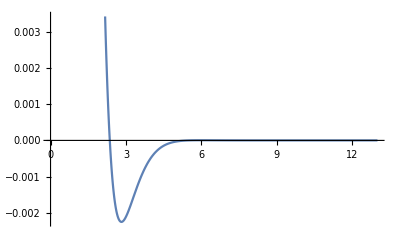

```mathematica
Plot[ⅇ^(-2 x)  Cos[x]+ⅇ^(-2 x)  Sin[x],{x,0,13}]
```

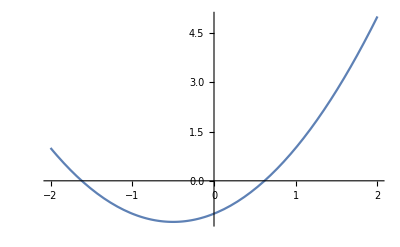

```mathematica
Plot[x^2+x-1,{x,-2,2}]
```

```mathematica
Solve[x^2+x-1==0,x]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
N[{{x->1/2 (-1-√5)},{x->1/2 (-1+√5)}}]
```

```mathematica
{{x->-1.618033988749895},{x->0.6180339887498949}}
```

```mathematica
Solve[D[x^2+x-1,x]==0,x]
```

{{x→-1/2}}

```mathematica
D[(y-a/2)^2==2b x,x,NonConstants->y]
```

2 (-a/2+y) D[y,x,NonConstants→{y}]==2 b